```mathematica
Needs["EDA`"]
```

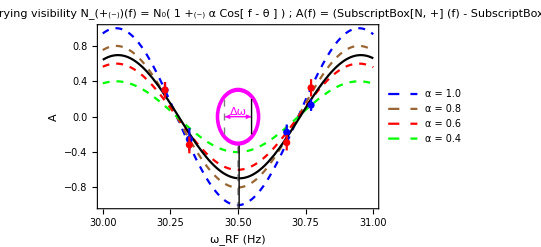

```mathematica
pt1[xx_,aa_]=N[5000(1+(aa Cos[3-7xx]))];
pt2[xx_,aa_]=N[5000(1-(aa Cos[3-7xx]))];
al[xx_,aa_]=(pt1[xx,aa]-pt2[xx,aa])/(pt1[xx,aa]+pt2[xx,aa]);
lineStyle={Thin,Gray,Dashed};
line1=Line[{{30.5,-1.2},{30.5,0}}];
lineStyle2={Thin,Black};
line2=Line[{{30.504,-1.2},{30.504,0}}];
lineStyle3={Thin,White};
disk1=Disk[{30.5,0},.9{.08,.32}];
lineStyle4={Thin,Magenta};
disk2=Disk[{30.5,0},{.08,.32}];
circle1=Circle[{30.5,0},{.08,.32}];
circle2=Circle[{30.5,0},.9{.08,.32}];
pttab={{30.23,{al[30.23,1],.5al[30.23,1]}},{30.32,{al[30.32,.8],-.5 al[30.32,.8]}},{30.68,{al[30.68,.6],-.5al[30.68,.6]}},{30.77,{al[30.77,.4],.5al[30.77,.4]}}};
pttab2={{30.23,{al[30.23,1],.3al[30.23,1]}},{30.32,{al[30.32,1],-.3 al[30.32,1]}},{30.68,{al[30.68,1],-.3al[30.68,1]}},{30.77,{al[30.77,1],.3al[30.77,1]}}};
Show[{Plot[{al[xx,1],al[xx,.8],al[xx,.6],al[xx,.4], 0.6961805217145691 Cos[3-7xx+0.047813907125757664]},{xx,30,31},Frame->True,PlotStyle->{{Dashed,Blue},{Dashed,Brown},{Dashed,Red},{Dashed,Green},Black},Epilog->{
{Directive[lineStyle],line1,Text[Style["ω_0",FontSize->Large],{30.45,-1.05}]},
{Directive[lineStyle2],line2,Text[Style["ω_0+Δω",FontSize->Large],{30.55,-1.05}]},
{Directive[lineStyle4],disk2},
{Directive[lineStyle3],disk1},
{Directive[lineStyle4],circle1,circle2,Text[Style["Δω",FontSize->Large],{30.5,0.05}]},
{Directive[lineStyle4],{Arrowheads[{-.02,.02}],Arrow[{{30.45,0},{30.55,0}}]}},
{Directive[lineStyle2],Line[{{30.55,-.2},{30.55,.2}}]},
{Directive[lineStyle],Line[{{30.45,-.2},{30.45,.2}}]}
},
FrameLabel->{"ω_RF (Hz)","A"},TicksStyle->Directive[FontSize->40],LabelStyle->{Black,18},ImageSize->{1200},PlotLegends->{"α = 1.0","α = 0.8","α = 0.6","α = 0.4"},PlotLabel->"Plot showing the asymmetry of Ramsey curve with varying visibility \n N_(+_(-))(f) = N_0( 1 +_(-) α Cos[ f - θ ] ) ; A(f) = (SubscriptBox[N, +] (f) - SubscriptBox[N, -] (f))/(SubscriptBox[N, +] (f) + SubscriptBox[N, -] (f))"],
EDAListPlot[pttab,pttab2,TicksStyle->Directive[FontSize->40],LabelStyle->{18},ImageSize->{1200},PlotStyle->{Blue,Red},PlotLabel->"Plot showing the asymmetry of Ramsey curve with varying visibility (NANOSc + USSA) \n N_(+_(-))(f) = N_0( 1 +_(-) α Cos[ f - θ ] ) ; A(f) = (SubscriptBox[N, +] (f) - SubscriptBox[N, -] (f))/(SubscriptBox[N, +] (f) + SubscriptBox[N, -] (f))"]}]
```